# Inlämningsuppgift #2 - Rapport

Seema Bashir , TIDAB, sfbashir@kth.se
Esra Salman , TIDAB, esras@kth.se

## Analysera data

Uppgift 1: Världens energikonsumtion år 2050.

## Sammanfattning

### Uppgift

Nedan finns data för världens energikonsumtion i TWh/år för olika energislag och för världens totala energikonsumtion. Anpassa lämpliga modeller (exponentialmodel, linjär model, etc) till datat nedan så att du kan förutsäga världens framtida energiandvändning. Använd funktionen FindFit för att hitta lämpliga koefficienter till modellerna. Tips: Förskjut tidsskalan med t→ t-1990 för att göra det enklare att hitta parametrarna i FindFit för icke-linjära anpassningar.

Uppskatta världens energikonsumtion år 2050.

### Resultat

Statistik för världskonsumtionen år 1990-2017 i TWh:

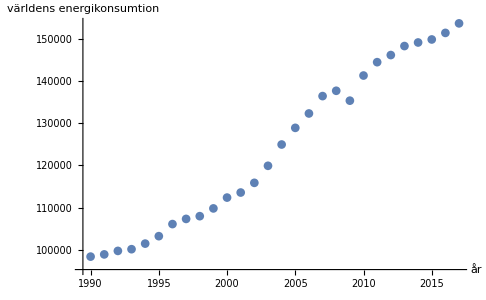

Med funktionen "FindFit" redovisas ett samband:

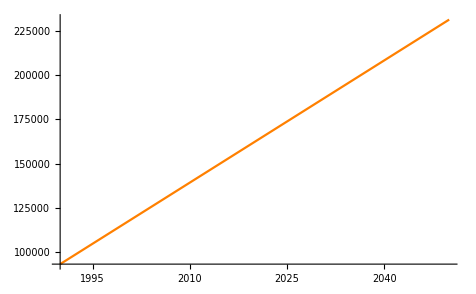

Önskade året 2050 inmatas därefter och en matematiskt resultat erhålls :

Året 2050, världens energikonsumtion: 231 747 TWh

## Kod

Världens totala energikonsumtion (TWh):

```mathematica
totalt1={{1990,98462.371847116},{1991.,98987.38143285},{1992.,99813.54908523199},{1993.,100216.423316547},{1994.,101537.18489717401},{1995.,103296.25934793001},{1996.,106154.70010584098},{1997.,107376.31135546902},{1998.,108022.57284627101},{1999.,109856.69807370701},{2000.,112416.258116246},{2001.,113610.635952175},{2002.,115901.223848704},{2003.,119930.15013616001},{2004.,124960.08846344402},{2005.,128897.75152416898},{2006.,132297.06634468702},{2007.,136405.679742778},{2008.,137662.43593741},{2009.,135324.15543267998},{2010.,141265.10288404},{2011.,144422.53459229},{2012.,146106.05926769998},{2013.,148234.8407671},{2014.,149077.14748530003},{2015.,149790.2224058},{2016.,151341.68784990002},{2017.,153595.6630277}}
```

{{1990,98462.4},{1991.,98987.4},{1992.,99813.5},{1993.,100216.},{1994.,101537.},{1995.,103296.},{1996.,106155.},{1997.,107376.},{1998.,108023.},{1999.,109857.},{2000.,112416.},{2001.,113611.},{2002.,115901.},{2003.,119930.},{2004.,124960.},{2005.,128898.},{2006.,132297.},{2007.,136406.},{2008.,137662.},{2009.,135324.},{2010.,141265.},{2011.,144423.},{2012.,146106.},{2013.,148235.},{2014.,149077.},{2015.,149790.},{2016.,151342.},{2017.,153596.}}

Visualisering av givna värden mellan åren 1990-2017 genom ListPlot-funktion:

```mathematica
p1 = ListPlot[totalt1, AxesLabel->{"år" , "världens energikonsumtion"}]
```

Förskjutning av tidsskalan:

```mathematica
{tot1, tot2}={a, b}/.FindFit[totalt1, {a (t-1990)+b}, {a, b}, t]
```

{2314.87,92855.}

Beräkning med funktionen etot:

```mathematica
etot[t_]:= tot1 (t-1990)+tot2
```

```mathematica
p2 = Plot [ etot[t], {t, 1990, 2050}, PlotStyle->Orange]
```

```mathematica
etot[2050]
```

231747.

## Diskussion

Resultatet visar hur en matematisk modell förutspår världens energikonsumtion år 2050. Först framställs värdena för givna åren 1990-2017, därefter används funktionen “FindFit” och förskjutning av tidsskalan “[totalt1, {a (t-1990)+b}, {a, b}, t]”. Det erhållna resultatet är 231747 TWh.

Uppgift 2: Uppskatta när olja som energikälla kan ersättas av förnybara energikällor?

## Sammanfattning

### Uppgift

Nedan finns data för världens energikonsumtion i TWh/år för olika energislag och för världens totala energikonsumtion . Anpassa lämpliga modeller (exponentialmodel, linjär model, etc) till datat nedan så att du kan förutsäga världens framtida energiandvändning . Använd funktionen FindFit för att hitta lämpliga koefficienter till modellerna . Tips : Förskjut tidsskalan med \!\(TraditionalForm\`t -> \ t - 1990\) för att göra det enklare att hitta parametrarna i FindFit för icke - linjära anpassningar.

Uppskatta när olja som energikälla kan ersättas av förnybara energikällor?

### Resultat

Biobränsle energikonsumtion år 1990 - 2017 :

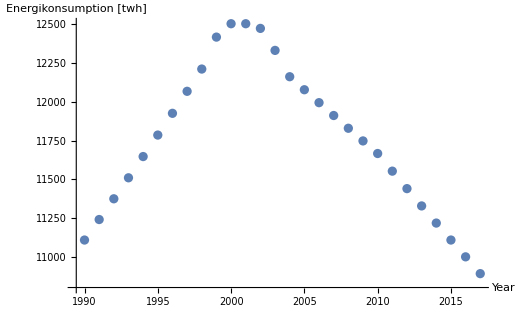

Biobränsle energikonsumtion år 2050:

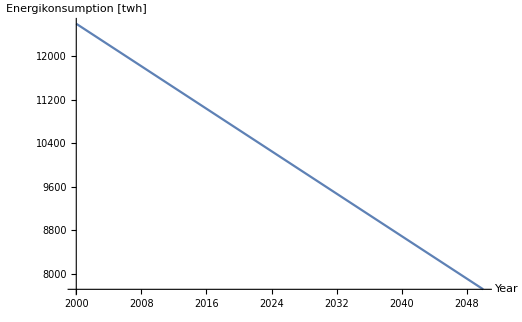

Andra Förnybara Energikällor energikonsumtion år1990-2017:

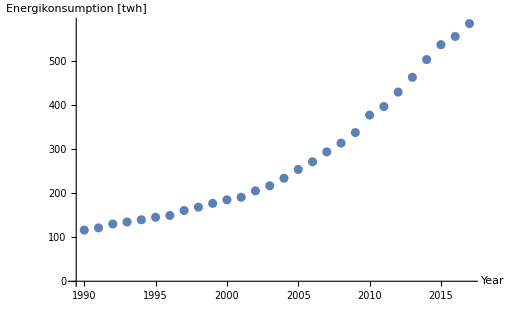

Andra Förnybara Energikällor energikonsumtion år 2050:

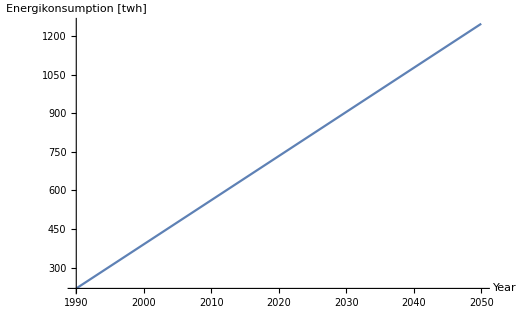

Vattenkraftverk energikonsumtion år 1990-2017:

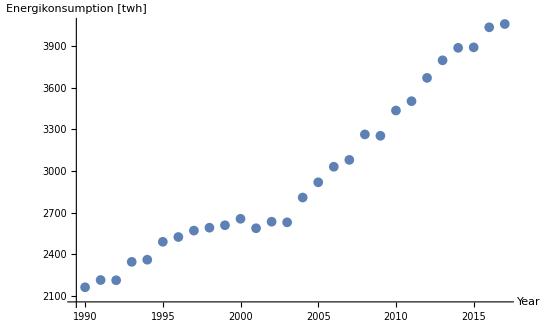

Vattenkraftverk energikonsumtion år 2050:

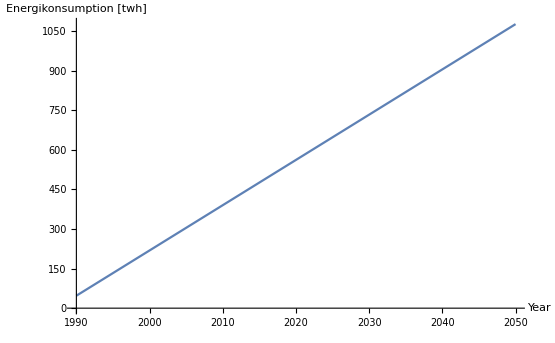

Vattenkraftverk energikonsumtion år 1990 - 2017:

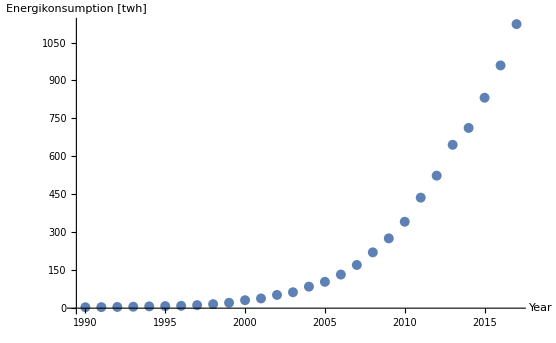

Vattenkraftverk energikonsumtion år 2050:

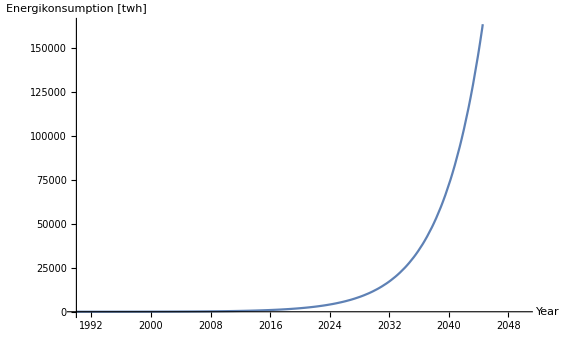

Solenergikonsumtion år 1990 - 2017:

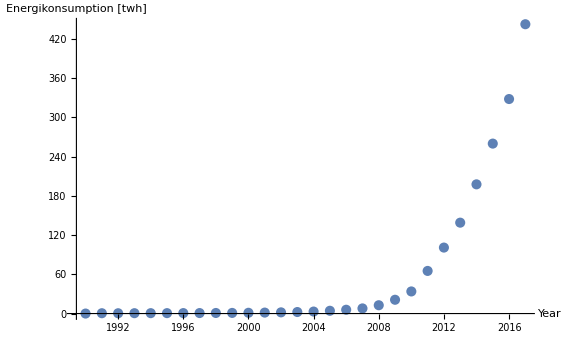

Solenergikonsumtion år 2050:

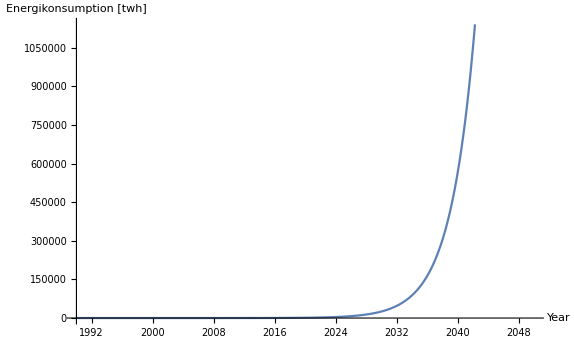

Grafernas summa:

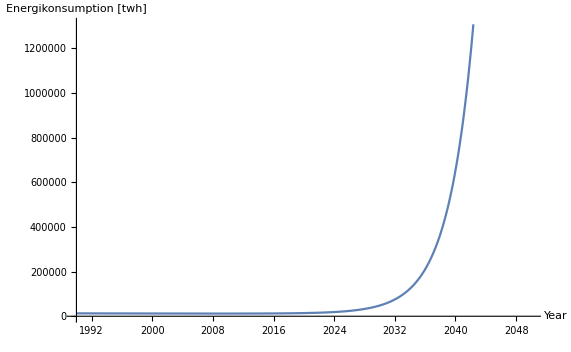

Olja energikonsumtion år 1990-2017:

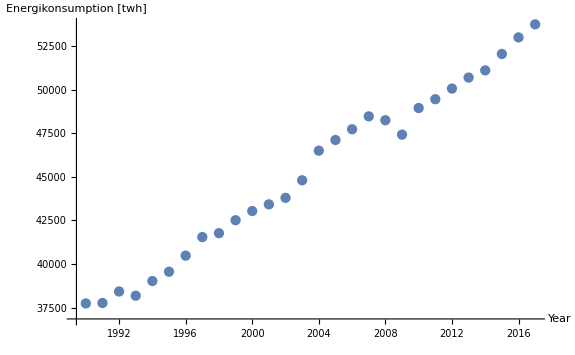

Olja energikonsumtion år 2050:

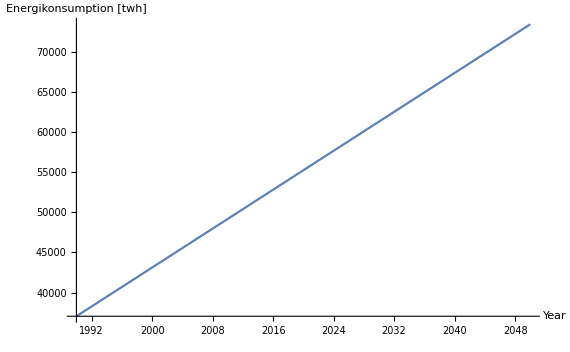

Oljeenergikonsumtion - och summan av förnybar energikonsumtion-grafer 2050:

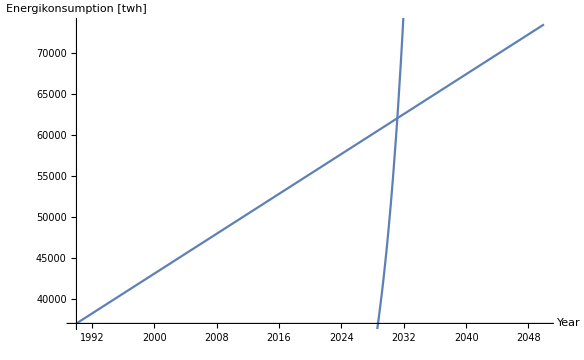

Olja som energikälla kan ersättas ca år 2031:

{t -> 2031.177053538398`}

## Kod

Biobränsle energikonsumtion år 1990 - 2050:

```mathematica
bioBränsle = {{1990.,11111.11111},{1991.,11242.7549},{1992.,11375.95839},{1993.,11510.74008},{1994.,11647.11865},{1995.,11785.11302},{1996.,11924.74234},{1997.,12066.02598},{1998.,12208.98355},{1999.,12414.05573},{2000.,12500.},{2001.,12500.},{2002.,12470.},{2003.,12328.70237},{2004.,12159.75217},{2005.,12076.14729},{2006.,11993.11724},{2007.,11910.65806},{2008.,11828.76583},{2009.,11747.43666},{2010.,11666.66667},{2011.,11553.3766},{2012.,11441.18663},{2013.,11330.0861},{2014.,11220.06442},{2015.,11111.11111},{2016.,11003.2158},{2017.,10895.32049}};
```

Först visualiseras Biobränsle energikonsumtionen med givna värden år 1990-2017:

```mathematica
ListPlot[bioBränsle, AxesLabel -> {"Year", "Energikonsumtion [twh]" }]
```

Eftersom grafen inledningsvis stiger och sedan sjunker tas åren 2000-2017 till beaktande:

Funktionen “take” inmatas för att visa värden under givna år:

```mathematica
bio = Take[bioBränsle, -18]
```

{{2000.,12500.},{2001.,12500.},{2002.,12470.},{2003.,12328.7},{2004.,12159.8},{2005.,12076.1},{2006.,11993.1},{2007.,11910.7},{2008.,11828.8},{2009.,11747.4},{2010.,11666.7},{2011.,11553.4},{2012.,11441.2},{2013.,11330.1},{2014.,11220.1},{2015.,11111.1},{2016.,11003.2},{2017.,10895.3}}

Grafen visar en linjär funktion vars formel beskrivs enligt y=kx+m. Funktionen “Findfit” inmatas för att erhålla k-värdet:

```mathematica
{a1, b1} = {a, b} /. FindFit[bio, {a(t-2000)+b}, {a,b }, t]
```

{-97.5393,12592.2}

```mathematica
bioTotal[t_]:= a1(t-1990)+b1
```

```mathematica
bioTotal[2000]
```

11616.8

Plot används för att rita grafen med funktionen “bioTotal”:

```mathematica
bioBränsleGraf = Plot[a1(t-2000)+b1, {t, 2000, 2050},AxesLabel -> {"Year", "Energikonsumtion [twh]"} ]
```

Andra förnybara energikällor energikonsumtion år 1990-2050, samma princip som ovan gäller:

```mathematica
andrafornybara={{1990.,116.4628246},{1991.,121.4122701},{1992.,130.3448548},{1993.,134.7069628},{1994.,139.8004029},{1995.,145.5958811},{1996.,149.6884804},{1997.,160.9528063},{1998.,168.4548712},{1999.,177.1371664},{2000.,185.2722028},{2001.,191.0179267},{2002.,205.6996386},{2003.,217.2027959},{2004.,234.3682046},{2005.,254.3922875},{2006.,271.7633551},{2007.,294.2977297},{2008.,314.3656167},{2009.,338.2157334},{2010.,378.0383427},{2011.,397.4546676},{2012.,430.3624386},{2013.,463.9825019},{2014.,504.3899227},{2015.,538.2067786},{2016.,556.9861292},{2017.,586.1710901}};
```

```mathematica
ListPlot[andrafornybara,AxesLabel->{"Year","Energikonsumtion [twh]"}]
```

```mathematica
{a2, b2} = {a, b} /. FindFit[andrafornybara, {a(t-2000)+b}, {a,b }, t]
```

{17.1558,218.767}

```mathematica
fornybaraTot[t_] :=a2(t-1990)+b2
```

```mathematica
andrafornybaraGraf = Plot[a2(t-1990) + b2, {t, 1990, 2050}, AxesLabel -> {"Year", "Energikonsumtion [twh]"}]
```

Vattenkraftverk, samma princip som ovan gäller:

```mathematica
vatten={{1990.,2161.045291},{1991.,2213.110915},{1992.,2211.503167},{1993.,2344.266136},{1994.,2359.685227},{1995.,2488.983207},{1996.,2523.481143},{1997.,2569.633113},{1998.,2590.551798},{1999.,2608.338262},{2000.,2654.953445},{2001.,2586.668594},{2002.,2633.835653},{2003.,2629.430399},{2004.,2808.226932},{2005.,2918.064831},{2006.,3030.307944},{2007.,3079.79887},{2008.,3263.589026},{2009.,3253.601171},{2010.,3435.905581},{2011.,3503.227091},{2012.,3671.297583},{2013.,3797.954118},{2014.,3887.930335},{2015.,3891.408797},{2016.,4036.073668},{2017.,4059.868393}};
```

```mathematica
ListPlot[vatten, AxesLabel -> {"Year", "Energikonsumtion [twh]"  }]
```

```mathematica
{a3, b3} = {a, b} /. FindFit[andrafornybara, {a(t-1990)+b}, {a,b }, t]
```

{17.1558,47.2089}

```mathematica
totalVatten [t_]:= a3(t-1990)+b3
```

```mathematica
vattenGraf =  Plot[a3(t-1990) + b3, {t, 1990, 2050}, AxesLabel -> {"Year", "Energikonsumtion [twh]"}]
```

Vindkraftverk, samma princip som ovan gäller:

```mathematica
vind={{1990.,3.632470516},{1991.,4.086706675},{1992.,4.733212019},{1993.,5.697568819},{1994.,7.122929844},{1995.,8.261923444},{1996.,9.204610762},{1997.,12.01757667},{1998.,15.91490057},{1999.,21.21534431},{2000.,31.41996387},{2001.,38.39098735},{2002.,52.33180737},{2003.,62.91691456},{2004.,85.11605376},{2005.,104.0868359},{2006.,132.8592792},{2007.,170.6860872},{2008.,220.5696719},{2009.,275.9292658},{2010.,341.5652412},{2011.,436.8034429},{2012.,523.8148612},{2013.,645.7219776},{2014.,712.4070431},{2015.,831.8262454},{2016.,959.4687163},{2017.,1122.74585}};
 ListPlot[vind, AxesLabel -> {"Year", "Energikonsumtion [twh]"  }]
```

```mathematica
{a4, b4} = {a, b}/. FindFit[vind, {a*Exp [b*(t-1990)]}, {a, b}, t]
```

{9.25548,0.179304}

```mathematica
vindTotal [t_]:= {a4*Exp[b4*(t-1990)]}
```

```mathematica
vindGraf = Plot[vindTotal[t], {t, 1990, 2050}, AxesLabel -> {"Year", "Energikonsumtion [twh]" }]
```

Solenergi, samma princip som ovan gäller:

```mathematica
sol={{1990.,0.},{1991.,0.505223075},{1992.,0.468615413},{1993.,0.556737928},{1994.,0.60006443},{1995.,0.640874386},{1996.,0.705278679},{1997.,0.756655499},{1998.,0.880289501},{1999.,0.965823997},{2000.,1.177935576},{2001.,1.463956125},{2002.,1.831247734},{2003.,2.3293707},{2004.,3.054656084},{2005.,4.249617769},{2006.,5.818328387},{2007.,7.864870878},{2008.,12.72162081},{2009.,21.09259048},{2010.,33.82948514},{2011.,65.21188479},{2012.,100.9252749},{2013.,139.0442186},{2014.,197.6716635},{2015.,260.0058008},{2016.,328.1826964},{2017.,442.6183606}};
```

```mathematica
ListPlot[sol, AxesLabel -> {"Year", "Energikonsumption [twh]"  }]
```

```mathematica
{a5, b5} = {a, b}/. FindFit[sol, {a*Exp [b*(t-1990)]}, {a, b}, t]
```

{0.104136,0.310299}

```mathematica
totalaSol [t_] := a5*Exp[b5*(t-1990)]
```

```mathematica
solGraf = Plot[totalaSol[t], {t, 1990, 2050}, AxesLabel -> {"Year", "Energikonsumtion [twh]" }]
```

Summa av alla ovan grafer:

```mathematica
totSummAvGrafer[t_]:= totalaSol [t]  +vindTotal [t]+ totalVatten [t] + fornybaraTot[t] + bioTotal[t]
```

```mathematica
totalFörnybarGraf  = Plot[totSummAvGrafer[t], {t, 1990, 2050},AxesLabel->{"Year","Energikonsumtion [twh]"}]
```

Olja, samma princip som ovan gäller:

```mathematica
olja={{1990.,37736.94729},{1991.,37763.14824},{1992.,38422.53103},{1993.,38179.42324},{1994.,39021.80173},{1995.,39555.43054},{1996.,40480.1731},{1997.,41544.67299},{1998.,41768.48384},{1999.,42510.09274},{2000.,43038.62001},{2001.,43421.10755},{2002.,43796.55068},{2003.,44803.21017},{2004.,46503.96733},{2005.,47115.72728},{2006.,47732.19992},{2007.,48471.73162},{2008.,48250.64229},{2009.,47422.36853},{2010.,48949.72046},{2011.,49455.27172},{2012.,50065.86499},{2013.,50698.38455},{2014.,51109.97172},{2015.,52053.27008},{2016.,53001.86598},{2017.,53752.27638}};
```

```mathematica
ListPlot[olja, AxesLabel -> {"Year", "Energikonsumtion [twh]"  }]
```

```mathematica
{a6, b6} = {a, b} /. FindFit[olja, {a(t-1990)+b}, {a,b }, t]
```

{606.174,37053.3}

```mathematica
oljaTot[t_] = a6(t-1990)+b6
```

37053.3+606.174 (-1990+t)

```mathematica
oljaGraf = Plot[a6(t-1990) + b6, {t, 1990, 2050}, AxesLabel -> {"Year", "Energikonsumtion [twh]"}]
```

Resultat av både olje- och förnybar energikällors grafer:

```mathematica
Show[oljaGraf,totalFörnybarGraf ]
```

```mathematica
FindRoot[oljaTot[t]==totSummAvGrafer[t],{t,2030}]
```

{t→2031.18}

## Diskussion

Resultatet visar grafer inom givna kategorier energikällor som visar ökning och minsking av de olika källorna. Slutlig graf påvisar att året som olja ersätts av förnybara energikällor sker ungefär år 2031. Oljegrafen visar en avtagande stagnering och efter grafernas skärningspunkt fortsätter en ökning i förnybar energi.

Uppgift 3: Uppskatta om/när världens energikonsumtion är CO_2 fri.

## Sammanfattning

### Uppgift

Nedan finns data för världens energikonsumtion i TWh/år för olika energislag och för världens totala energikonsumtion . Anpassa lämpliga modeller (exponentialmodel, linjär model, etc) till datat nedan så att du kan förutsäga världens framtida energiandvändning . Använd funktionen FindFit för att hitta lämpliga koefficienter till modellerna . Tips : Förskjut tidsskalan med \!\(TraditionalForm\`t -> \ t - 1990\) för att göra det enklare att hitta parametrarna i FindFit för icke - linjära anpassningar .

Uppskatta om/när världens energikonsumtion är CO_2 fri?

### Resultat

Kol energikonsumtion år 1990 - 2017 :

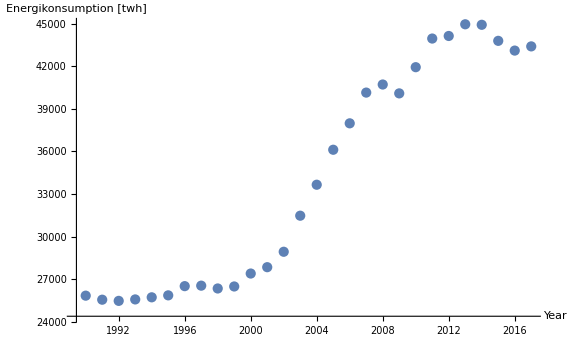

Kol energikonsumtion år 2050:

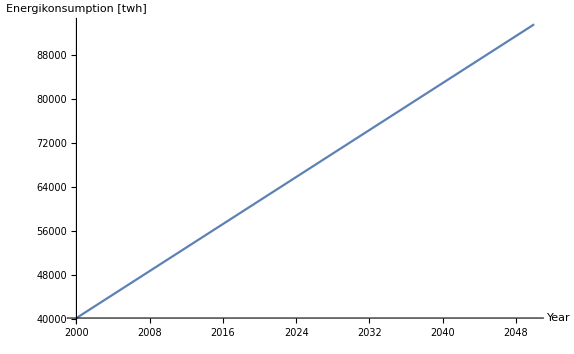

Olja energikonsumtion år 1990-2017:

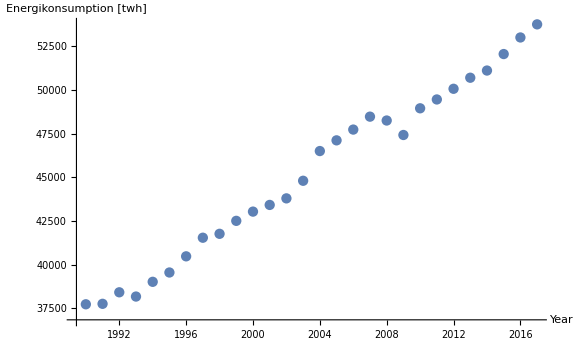

Olja energikonsumtion år 2050:

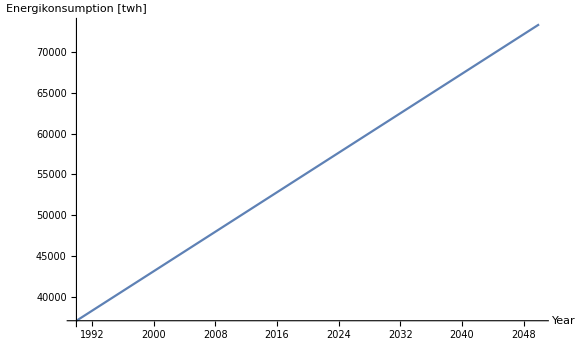

Naturgas energikonsumtion år 1990-2017:

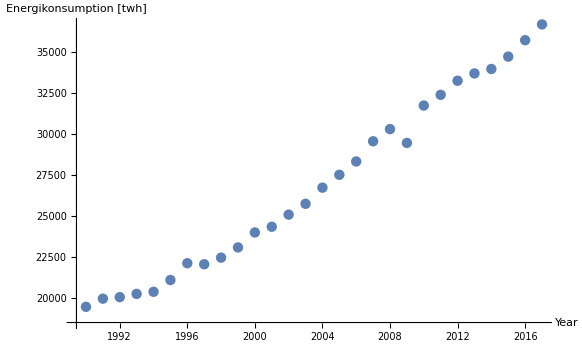

Naturgas energikonsumtion år 2050:

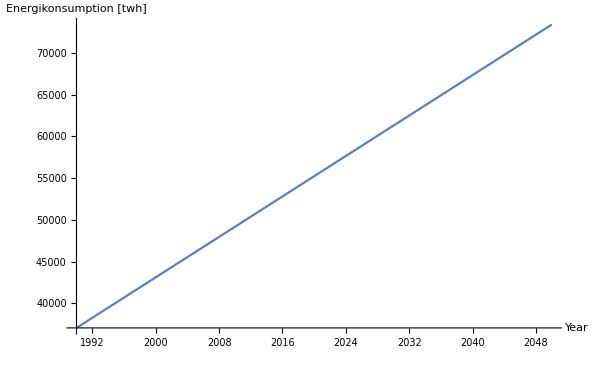

Kärnkraftverk energikonsumtion år 1990-2017:

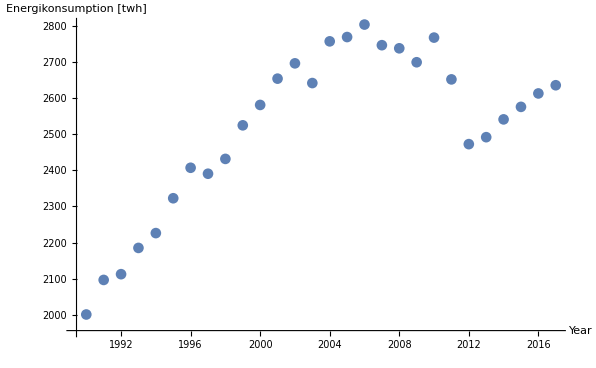

Kärnkraftverk energikonsumtion år 2050:

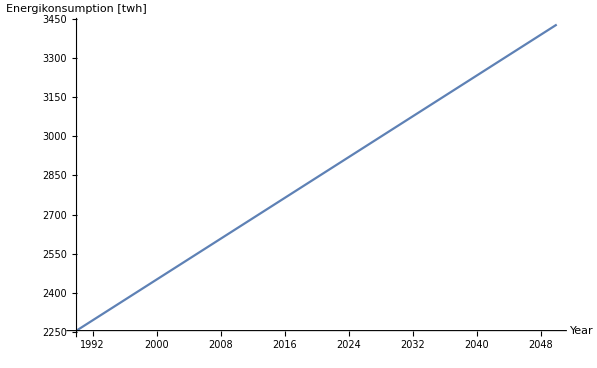

Total icke CO2 år 2050:

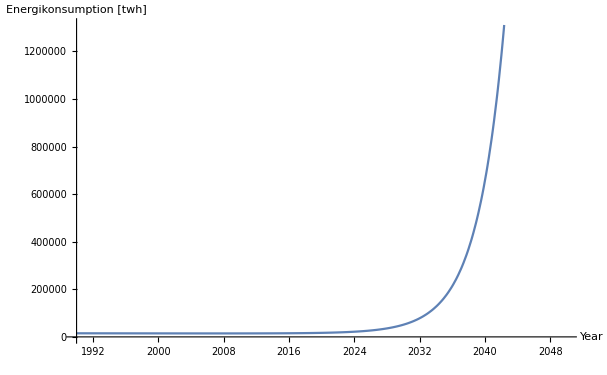

Total CO2 år 2050:

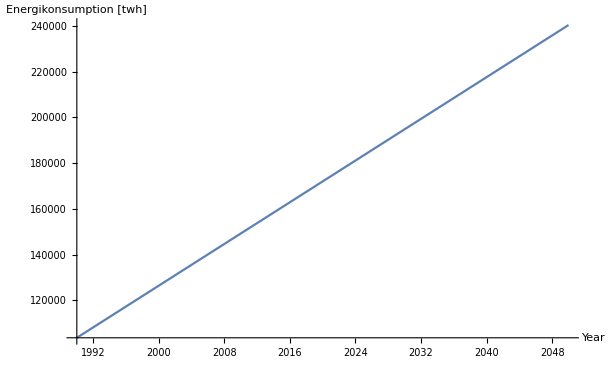

Summa av två ovan grafer år 2050:

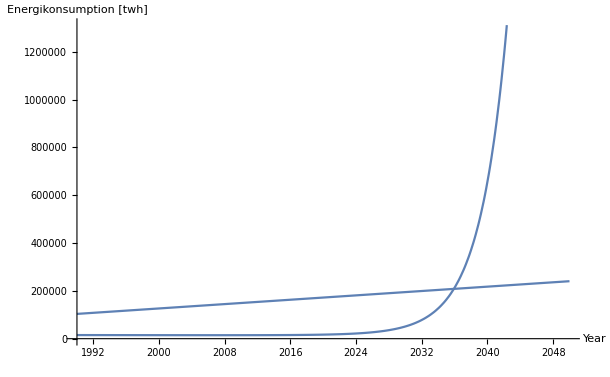

```mathematica
FindRoot[ickeC02[t] ==C02Funktioner[t],{t,2030}]
```

{t→2035.91}

Ungefär år 2036 beräknas världens energikonsumtion vara CO2 fri.

## Kod

```mathematica
kol={{1990.,25845.88485},{1991.,25561.41954},{1992.,25478.81089},{1993.,25580.92144},{1994.,25729.64169},{1995.,25867.8533},{1996.,26516.28457},{1997.,26549.71899},{1998.,26351.79429},{1999.,26492.77461},{2000.,27403.94562},{2001.,27851.05371},{2002.,28936.6423},{2003.,31475.58334},{2004.,33656.31109},{2005.,36118.94545},{2006.,37979.81684},{2007.,40143.91171},{2008.,40712.5427},{2009.,40088.33994},{2010.,41932.74507},{2011.,43948.96889},{2012.,44129.62497},{2013.,44953.01385},{2014.,44916.83781},{2015.,43786.8458},{2016.,43101.23216},{2017.,43397.13549}};
```

Visualisering av kolbränslets energikonsumtion med givna värden år 1990-2017:

```mathematica
ListPlot[kol, AxesLabel -> {"Year", "Energikonsumtion [twh]"  }]
```

Grafen är konstant i början, därmed blir de 15 åren mellan år 2000-2017 relevanta:

Funktionen “take” inmatas för att erhålla värden under givna år:

```mathematica
coal = Take[kol, -18]
```

```mathematica
{{2000.,27403.94562},{2001.,27851.05371},{2002.,28936.6423},{2003.,31475.58334},{2004.,33656.31109},{2005.,36118.94545},{2006.,37979.81684},{2007.,40143.91171},{2008.,40712.5427},{2009.,40088.33994},{2010.,41932.74507},{2011.,43948.96889},{2012.,44129.62497},{2013.,44953.01385},{2014.,44916.83781},{2015.,43786.8458},{2016.,43101.23216},{2017.,43397.13549}}
```

{{2000.,27403.9},{2001.,27851.1},{2002.,28936.6},{2003.,31475.6},{2004.,33656.3},{2005.,36118.9},{2006.,37979.8},{2007.,40143.9},{2008.,40712.5},{2009.,40088.3},{2010.,41932.7},{2011.,43949.},{2012.,44129.6},{2013.,44953.},{2014.,44916.8},{2015.,43786.8},{2016.,43101.2},{2017.,43397.1}}

Grafen är linjär och följer räta linjen formel -> y=kx+m. Funktionen “FindFit” inmatas för att erhålla k-värdet:

```mathematica
{a7, b7} = {a, b} /. FindFit[coal, {a(t-2000)+b}, {a,b }, t]
```

{1066.95,29516.1}

```mathematica
kolTotal[t_]:= a7(t-1990)+b7
```

Plot används för att visualisera funktion “KolTotal” på en graph:

```mathematica
kolGraf = Plot[kolTotal[t], {t, 2000, 2050}, AxesLabel -> {"Year", "Energikonsumtion [twh]" }]
```

```mathematica
olja={{1990.,37736.94729},{1991.,37763.14824},{1992.,38422.53103},{1993.,38179.42324},{1994.,39021.80173},{1995.,39555.43054},{1996.,40480.1731},{1997.,41544.67299},{1998.,41768.48384},{1999.,42510.09274},{2000.,43038.62001},{2001.,43421.10755},{2002.,43796.55068},{2003.,44803.21017},{2004.,46503.96733},{2005.,47115.72728},{2006.,47732.19992},{2007.,48471.73162},{2008.,48250.64229},{2009.,47422.36853},{2010.,48949.72046},{2011.,49455.27172},{2012.,50065.86499},{2013.,50698.38455},{2014.,51109.97172},{2015.,52053.27008},{2016.,53001.86598},{2017.,53752.27638}};
```

Visualisering av oljans energikonsumtion med givna värden år 1990-2017:

```mathematica
ListPlot[olja, AxesLabel -> {"Year", "Energikonsumtion [twh]"  }]
```

Grafen är linjär och följer räta linjen formel -> y=kx+m. Funktionen “FindFit” inmatas för att erhålla k-värdet:

```mathematica
{a8, b8} = {a, b} /. FindFit[olja, {a(t-1990)+b}, {a,b }, t]
```

{606.174,37053.3}

```mathematica
oljaTotal[t_]:= a8(t-1990)+b8
```

Funktionen “oljaTotal” visualiseras på en graf.

```mathematica
oljaGraf = Plot[oljaTotal[t], {t, 1990, 2050}, AxesLabel -> {"Year", "Energikonsumtion [twh]" }]
```

Visualisering av naturgasens energikonsumtion med givna värden år 1990-2017:

```mathematica
naturgas={{1990.,19486.64542},{1991.,19984.58677},{1992.,20076.92098},{1993.,20275.09431},{1994.,20405.36342},{1995.,21121.78818},{1996.,22143.41796},{1997.,22082.05319},{1998.,22485.93806},{1999.,23107.57158},{2000.,24019.89227},{2001.,24367.11133},{2002.,25108.12839},{2003.,25769.17552},{2004.,26752.16794},{2005.,27537.09099},{2006.,28347.57835},{2007.,29580.25097},{2008.,30321.37836},{2009.,29477.9263},{2010.,31759.12422},{2011.,32410.44868},{2012.,33270.53388},{2013.,33714.94785},{2014.,33986.84723},{2015.,34741.88349},{2016.,35741.82987},{2017.,36703.96587}};
```

```mathematica
ListPlot[naturgas, AxesLabel -> {"Year", "Energikonsumption [twh]"  }]
```

Grafen är linjär och följer räta linjen formel -> y=kx+m. Funktionen “FindFit” inmatas för att erhålla k-värdet:

```mathematica
{a9, b9} = {a, b} /. FindFit[olja, {a(t-1990)+b}, {a,b }, t]
```

{606.174,37053.3}

```mathematica
naturTotal[t_]:= a9(t-1990)+b9
```

Plot används för att rita grafen till funktionen “naturTotal”:

```mathematica
naturGasGraf =  Plot[naturTotal[t], {t, 1990, 2050}, AxesLabel -> {"Year", "Energikonsumtion [twh]" }]
```

Visualisering av kärnkraftverkens energikonsumtion med givna värden år 1990-2017:

```mathematica
karnkraft={{1990.,2000.642591},{1991.,2096.356868},{1992.,2112.277946},{1993.,2185.016841},{1994.,2226.050783},{1995.,2322.592422},{1996.,2407.002623},{1997.,2390.480054},{1998.,2431.571247},{1999.,2524.546817},{2000.,2580.976669},{2001.,2653.821898},{2002.,2696.204132},{2003.,2641.599256},{2004.,2757.124087},{2005.,2769.046942},{2006.,2803.605088},{2007.,2746.479825},{2008.,2737.860822},{2009.,2699.245242},{2010.,2767.507814},{2011.,2651.771616},{2012.,2472.44864},{2013.,2491.705601},{2014.,2541.027341},{2015.,2575.664304},{2016.,2612.83283},{2017.,2635.561104}};
```

```mathematica
ListPlot[karnkraft, AxesLabel -> {"Year", "Energikonsumtion [twh]"  }]
```

Grafen är linjär och följer räta linjen formel -> y=kx+m. Funktionen “FindFit” inmatas för att erhålla k-värdet:

```mathematica
{a10, b10} = {a, b} /. FindFit[karnkraft, {a(t-1990)+b}, {a,b }, t]
```

{19.5573,2254.94}

```mathematica
karnkraftTotal[t_]:= a10(t-1990)+b10
```

Plot används för att rita grafen till funktion karnkraftTotal.

```mathematica
karnkraftGraf =  Plot[karnkraftTotal[t], {t, 1990, 2050}, AxesLabel -> {"Year", "Energikonsumtion [twh]" }]
```

```mathematica
ickeC02[t_] := totSummAvGrafer[t] + karnkraftTotal[t]
```

En funktion ickeC02 skapas genom att addera den totala summa av grafer och kärnkraft. Denna funktion innehåller energikonsumptionen som inte släpper koldioxid:

```mathematica
C02Funktioner[t_]:= naturTotal[t] + oljaTotal[t] + kolTotal[t]
```

En annan funktion CO2funktioner skapas genom att addera naturgas energikonsuptionen, olja energikonsumption och kol energikonsuptionen, alltså alla energikällor som släpper koldioxid.

```mathematica
totalickeC02Graf  = Plot[ickeC02[t], {t, 1990, 2050},AxesLabel->{"Year","Energikonsumtion [twh]"}]
```

Plot används för att rita upp grafen till funktionen ickeC02

```mathematica
totalC02FunktionGraf = Plot[C02Funktioner[t], {t, 1990, 2050},AxesLabel->{"Year","Energikonsumtion [twh]"}]
```

Plot används för att rita upp grafen till funktionen CO2funktioner.

```mathematica
Show[totalickeC02Graf  ,totalC02FunktionGraf  ]
```

Show används för att visualisera både grafen till “totalickeCO2Graf” och “totalCO2FunktionGraf”

```mathematica
FindRoot[ickeC02[t] ==C02Funktioner[t],{t,2030}]
```

“Findroot” söker numerisk lösning, därför används för att finna skärningspunkten till graferna för IckeCO2 och CO2.

{t→2035.91}

## Diskussion

Resultatet visar samtliga grafer för ickeCO2-energikällor och CO2-energikällor, där skärningspunkten är runt år 2036. Därefter ökar ickeC02 energikällor markant samtidigt som CO2 behåller en någorlunda stabil låg utveckling - därmed kan CO2 avvecklas helt.

Uppgift 4: Vilket förnybart energislag uppskattas vara viktigast år 2050?

## Sammanfattning

### Uppgift

Nedan finns data för världens energikonsumtion i TWh/år för olika energislag och för världens totala energikonsumtion . Anpassa lämpliga modeller (exponentialmodel, linjär model, etc) till datat nedan så att du kan förutsäga världens framtida energiandvändning . Använd funktionen FindFit för att hitta lämpliga koefficienter till modellerna . Tips : Förskjut tidsskalan med \!\(TraditionalForm\`t -> \ t - 1990\) för att göra det enklare att hitta parametrarna i FindFit för icke - linjära anpassningar .

Vilket förnybart energislag uppskattas vara viktigast år 2050?

### Resultat

Andra förnybara energikällor energikonsumtion år 1990 - 2017 :

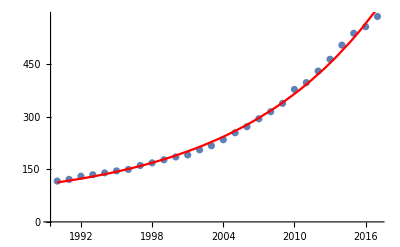

Andra förnybara energikällor energikonsumtion år 1990 - 2100 :

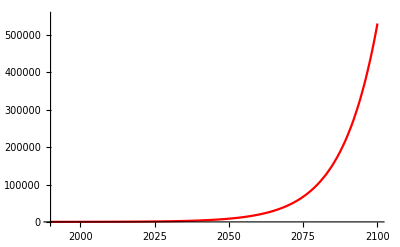

Vattenkraftverk energikonsumtion år 1990 - 2017 :

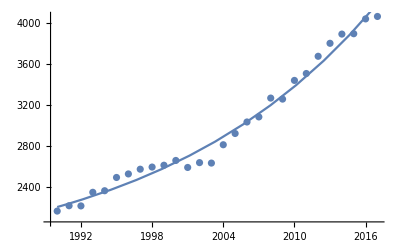

Vattenkraftverk energikonsumtion år 1990 - 2100 :

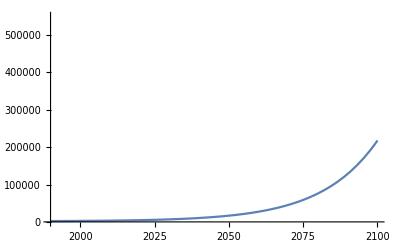

Vindkraftverk energikonsumtion år 1990 - 2017 :

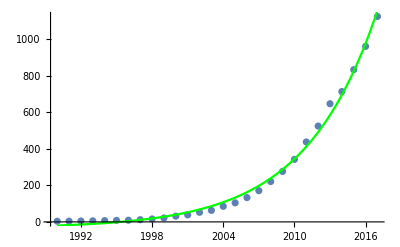

Vindkraftverk energikonsumtion år 1990 - 2100 :

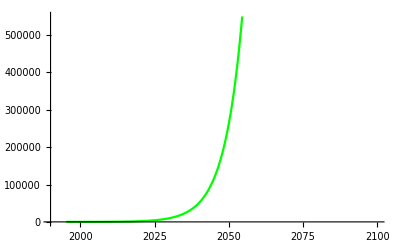

Solenergikonsumtion år 1990 - 2017 :

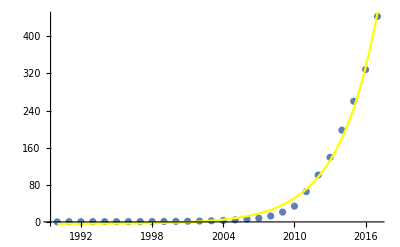

Solenergikonsumtion år 1990 - 2100:

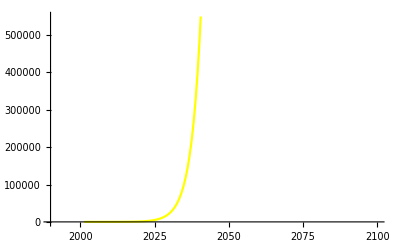

Summan av alla grafer år 1990 - 2100:

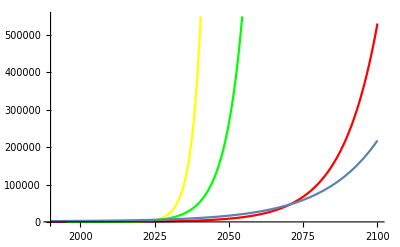

```mathematica
Show[grafandra, grafsol, grafvin, grafvatt]
```

Resultatet visar att solel kommer vara det viktigaste energikällan år 2050.

## Kod

Samtliga grafer är beräknade i tidigare uppgifter, nedan sker en plottring av dessa.

Andra förnybara energikällor:

```mathematica
andrafornybara={{1990.,116.4628246},{1991.,121.4122701},{1992.,130.3448548},{1993.,134.7069628},{1994.,139.8004029},{1995.,145.5958811},{1996.,149.6884804},{1997.,160.9528063},{1998.,168.4548712},{1999.,177.1371664},{2000.,185.2722028},{2001.,191.0179267},{2002.,205.6996386},{2003.,217.2027959},{2004.,234.3682046},{2005.,254.3922875},{2006.,271.7633551},{2007.,294.2977297},{2008.,314.3656167},{2009.,338.2157334},{2010.,378.0383427},{2011.,397.4546676},{2012.,430.3624386},{2013.,463.9825019},{2014.,504.3899227},{2015.,538.2067786},{2016.,556.9861292},{2017.,586.1710901}};
```

```mathematica
nlmandra=NonlinearModelFit[andrafornybara,a *b^x+c,{a,b,c},x,MaxIterations->Infinity]
Show[ListPlot@andrafornybara,Plot[nlmandra[x],{x,1990,2100}, PlotStyle->Red]]
```

FittedModel[52.8316+2.21665×10^-70 1.08616^x]

```mathematica
andra[x_]:= 52.83161404472271+2.2166465980315373*^-70 1.0861629170910878^x
```

```mathematica
grafandra = Plot[andra[x], {x, 1990, 2100}, PlotRange-> {{1990,2100},{0,550000}}, PlotStyle->Red]
```

Vattenkraftverk:

```mathematica
vatten={{1990.,2161.045291},{1991.,2213.110915},{1992.,2211.503167},{1993.,2344.266136},{1994.,2359.685227},{1995.,2488.983207},{1996.,2523.481143},{1997.,2569.633113},{1998.,2590.551798},{1999.,2608.338262},{2000.,2654.953445},{2001.,2586.668594},{2002.,2633.835653},{2003.,2629.430399},{2004.,2808.226932},{2005.,2918.064831},{2006.,3030.307944},{2007.,3079.79887},{2008.,3263.589026},{2009.,3253.601171},{2010.,3435.905581},{2011.,3503.227091},{2012.,3671.297583},{2013.,3797.954118},{2014.,3887.930335},{2015.,3891.408797},{2016.,4036.073668},{2017.,4059.868393}};
```

```mathematica
nlmvatten=NonlinearModelFit[vatten,a *b^x+c,{a,b,c},x,MaxIterations->Infinity]
Show[ListPlot@vatten,Plot[nlmvatten[x],{x,1990,2100}]]
```

FittedModel[1582.3+5.84475×10^-44 1.0547^x]

```mathematica
vatt[x_]:= 1582.301329239329+5.844747307069365*^-44 1.054697348919932^x
```

```mathematica
grafvatt = Plot[vatt[x], {x, 1990, 2100}, PlotRange-> {{1990,2100},{0,550000}}]
```

Vindkraftverk:

```mathematica
vind={{1990.,3.632470516},{1991.,4.086706675},{1992.,4.733212019},{1993.,5.697568819},{1994.,7.122929844},{1995.,8.261923444},{1996.,9.204610762},{1997.,12.01757667},{1998.,15.91490057},{1999.,21.21534431},{2000.,31.41996387},{2001.,38.39098735},{2002.,52.33180737},{2003.,62.91691456},{2004.,85.11605376},{2005.,104.0868359},{2006.,132.8592792},{2007.,170.6860872},{2008.,220.5696719},{2009.,275.9292658},{2010.,341.5652412},{2011.,436.8034429},{2012.,523.8148612},{2013.,645.7219776},{2014.,712.4070431},{2015.,831.8262454},{2016.,959.4687163},{2017.,1122.74585}};
```

```mathematica
nlmvind=NonlinearModelFit[vind,a *b^x+c,{a,b,c},x,MaxIterations->Infinity]
Show[ListPlot@vind,Plot[nlmvind[x],{x,1990,2100}, PlotStyle->Green]]
```

FittedModel[-34.0923+4.89156×10^-141 1.17785^x]

```mathematica
vin[x_]:= -34.09225301823332+4.8915631764593455*^-141 1.1778463584558114^x
```

```mathematica
grafvin = Plot[vin[x], {x, 1990, 2100}, PlotRange-> {{1990,2100},{0,550000}}, PlotStyle->Green]
```

Solel:

```mathematica
sol={{1990.,0.},{1991.,0.505223075},{1992.,0.468615413},{1993.,0.556737928},{1994.,0.60006443},{1995.,0.640874386},{1996.,0.705278679},{1997.,0.756655499},{1998.,0.880289501},{1999.,0.965823997},{2000.,1.177935576},{2001.,1.463956125},{2002.,1.831247734},{2003.,2.3293707},{2004.,3.054656084},{2005.,4.249617769},{2006.,5.818328387},{2007.,7.864870878},{2008.,12.72162081},{2009.,21.09259048},{2010.,33.82948514},{2011.,65.21188479},{2012.,100.9252749},{2013.,139.0442186},{2014.,197.6716635},{2015.,260.0058008},{2016.,328.1826964},{2017.,442.6183606}};
```

```mathematica
nlmsol=NonlinearModelFit[sol,a *b^x+c,{a,b,c},x,MaxIterations->Infinity]
Show[ListPlot@sol,Plot[nlmsol[x],{x,1990,2100},  PlotStyle-> Yellow]]
```

FittedModel[-4.06763+3.43526×10^-262 1.35191^x]

```mathematica
so[x_]:= -4.067629489773608+3.4352594891652687*^-262 1.35191116065072^x
```

```mathematica
grafsol = Plot[so[x], {x, 1990, 2100}, PlotRange-> {{1990,2100},{0,550000}}, PlotStyle->Yellow]
```

Plottring av samtliga grafer:

```mathematica
Show[grafandra, grafsol, grafvin, grafvatt]
```

## Diskussion

Resultat visar att solel blir det viktigaste energikällan år 2050, då den ökar markant runt år 2035. Även vindkraftverk får en markant ökning, dock senare runt år 2050 - då har solel redan dominerat i energiförbrukningen. Andra energikällor och vattenkraftverk följer sen segare utveckling och tar fart runt år 2080.

Uppgift 5: Vad har val av modell för betydelse?

## Diskussion

Det är önskvärt att välja modeller som visar datan tydligt och hur den förändras över tid. Datmängderna visar i just detta fall hur nämnda energikällor både ökat och minskat mellan åren 1990-2017. Med hjälp av den statstik så görs en uppskattning på hur det utveckling eller avveckling av energikällor ser ut framtill år 2050. Några exempel på hur vissa energikällor hade kunnat visas i andra typer av grafer demonstreras enligt följande:
Vindkraftverk ökade markant och kan illustreras i en exponentiell funktion - dock kommer inte noggrannhet finnas, då tillväxten inte visas tydligt och energikällans behovsanalys blir otydlig år 2050. 
Därmed önskas en modell som visar tydlig ökning eller minskning, i en både god visualisering och med tydliga värden.

Uppgift 6: Är ovanstående förutsägelser rimliga? Är förutsägelserna rimliga till 2030?

## Diskussion

Eftersom världen går mot en alltmer förnybar energiförbrukning, visar modellerna en sannolik utveckling. Vid år 2030 ökar solel markant som lyfter frågor, då ingen energikälla är evig och däför sannolikt att mätningarna avtar. Övriga energikällor förhåller sig till en någorlunda linjär och oextrem ökning/minsking (med undantag biogas). Dock är verkligheten oförutsägbar, även om mätningar och närmevärden erhålls.

Uppgift 7: Vilka felkällor finns?

## Diskussion

Som nämnt under fråga 6, så är dessa värden inte exakta. Exempelvis så ökar vind-och solel markant, det är en osannolik hållbarhet. Samtliga resultat är endast hypotetiska förutsägelser på framtidens utmaningar. Den mänskliga faktorn är en självklar felkälla, men även mätverktygen i Mathematica kan drabbas av systemfel, även datorverktyg och möjligtvis beräkna fel resultat.

Uppgift 8: Världens totala energiförbrukning år 2021 var 165319 TWh. Hur stämmer det med er modell? Kommentera!

## Diskussion

Modellen visar i själva verket att den totala energiförbrukningen år 2021 var ungefär 165000 TWh.